```mathematica
CalcTau[nc_,θ_,h_,n0_,tf_]:=(sol = NDSolve[{n'[t]==(a*K^2+s(n[t]-1)(n[t]-2))/((n[t]-1)(n[t]-2)+K^2)-n[t]/.{s-> (3*nc^3*(θ+h)+nc*x^2+x^3)/(3*nc^2*θ+x^2),K->N[Sqrt[(3*x^2+1)/4]], a->((3*x^2+1)*(3*nc^3*(θ+h)+nc*x^2+x^3)-4*x^5)/((3*x^2+1)*(3*nc^2*θ+x^2))}/.{ x->2*nc-3}, n[0]==n0},n,{t,0,tf}];{NIntegrate[Evaluate[((n[t]-n[tf])/(n[0]-n[tf]))/.sol],{t,0,tf}][[1]], sol})
```

```mathematica
CalcTauIsing[nc_,θ_,h_,n0_,tf_]:=(sol = NDSolve[{m'[t]==-1/3 m[t]^3-θ*m[t]+h, m[0]==(n0-nc)/nc},m,{t,0,tf}];{NIntegrate[Evaluate[((m[t]-m[tf])/(m[0]-m[tf]))/.sol],{t,0,tf}][[1]], sol})
```

```mathematica
tautab=Table[{hf,CalcTau[2000,0,hf,3478,200][[1]]/√2},{hf,-0.1,0.09,0.005}];
```

```mathematica
tauNeghtab=Table[{hf,CalcTau[2000,0,hf,771.73,200][[1]]/√2},{hf,-0.1,0.1,0.005}];
```

```mathematica
tauIsingNeghtab=Table[{hf,CalcTauIsing[2000,0,hf,771.73,200][[1]]},{hf,-0.1,0.1,0.005}];
```

```mathematica
tauIsingtab=Table[{hf,CalcTauIsing[2000,0,hf,3478,200][[1]]},{hf,-0.1,0.1,0.005}];
```

```mathematica
thetatab = Table[{tf,CalcTau[2000,tf,0,3009.8,200][[1]]},{tf,-0.1,0.1,0.005}];
```

```mathematica
thetaIsingtab = Table[{tf,CalcTauIsing[2000,tf,0,3009.8,200][[1]]},{tf,-0.1,0.1,0.005}];
```

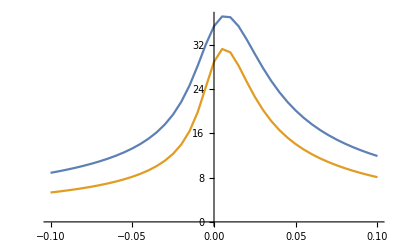

```mathematica
ListPlot[{thetatab,thetaIsingtab},Joined->True]
```

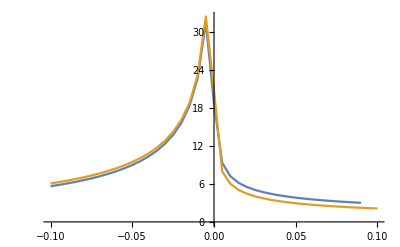

```mathematica
ListPlot[{tautab,tauIsingtab}, Joined->True]
```

```mathematica
Export["/Users/ereza/Documents/Research/Mugler/GillespieSchlogl/tempquench.csv",tautab]
```

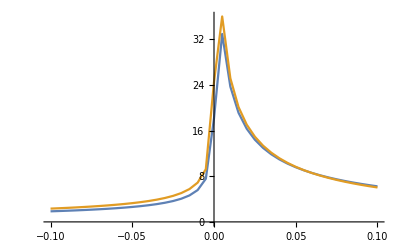

```mathematica
ListPlot[{tauNeghtab,tauIsingNeghtab}, Joined->True, PlotRange->All]
```

```mathematica
Export["/Users/ereza/Documents/Research/Mugler/GillespieSchlogl/tempIsing.csv",tauIsingtab]
Export["/Users/ereza/Documents/Research/Mugler/GillespieSchlogl/tempNeg.csv",tauNeghtab]
Export["/Users/ereza/Documents/Research/Mugler/GillespieSchlogl/tempIsingNeg.csv",tauIsingNeghtab]
```

/Users/ereza/Documents/Research/Mugler/GillespieSchlogl/tempIsing.csv

/Users/ereza/Documents/Research/Mugler/GillespieSchlogl/tempNeg.csv

/Users/ereza/Documents/Research/Mugler/GillespieSchlogl/tempIsingNeg.csv

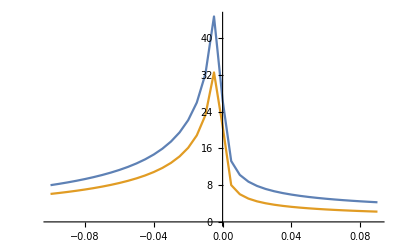

167.839

```mathematica
ListPlot[{tautab, tauIsingtab}, Joined->True, PlotRange->All]
```

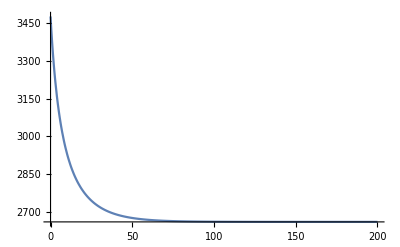

167.839

```mathematica
Plot[Evaluate[n[t]/.sol],{t,0,200},PlotRange->All]
```

```mathematica
example = CalcTau[2000,0,-0.01,3532,200]
```

{31.6865,{{n→InterpolatingFunction[{{0., 200.}}, <>]}}}

```mathematica
tab = Table[{t,Evaluate[n[t]/.example[[2]]][[1]]}, {t,0,200,0.025}]
```

{{0.,3532.},{0.025,3527.96},{0.05,3523.94},{0.075,3519.95},{0.1,3515.99},7992,{199.925,1405.98},{199.95,1405.98},{199.975,1405.98},{200.,1405.98}}
 |  |  |  |

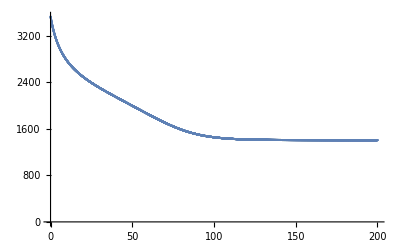

```mathematica
ListPlot[tab]
```

```mathematica
Export["/Users/ereza/Documents/Research/Mugler/GillespieSchlogl/example.csv",tab]
```

/Users/ereza/Documents/Research/Mugler/GillespieSchlogl/example.csv

```mathematica
(*params={s-> (3*nc^3*(θ+h)+nc*x^2+x^3)/(3*nc^2*θ+x^2),K->N[Sqrt[(3*x^2+1)/4]], a->((3*x^2+1)*(3*nc^3*(θ+h)+nc*x^2+x^3)-4*x^5)/((3*x^2+1)*(3*nc^2*θ+x^2))}/.{ x->2*nc-3, θ->0,h->0.01}/.{nc->2000}
sol = NDSolve[{n'[t]==(a*K^2+s(n[t]-1)(n[t]-2))/((n[t]-1)(n[t]-2)+K^2)-n[t]/.params, n[0]==3478},n,{t,0,200}];
τ=NIntegrate[Evaluate[((n[t]-n[200])/(n[0]-n[200]))/.sol],{t,0,200}][[1]]*)
```